## Basic Definitions

```mathematica
(*PacletInstall["Wolfram/QuantumFramework"]*)
```

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

```mathematica
(* Basis and operators *)
basis[L_]:=QuantumBasis[2,L];
X[i_]:=QuantumOperator["X",{i}];
Y[i_]:=QuantumOperator["Y",{i}];
Z[i_]:=QuantumOperator["Z",{i}];
```

```mathematica
(* MPS representation of state *)
vars[L_]:=Table[Subscript[σ, i],{i,1,L}]
sumRange[L_]:=Sequence@@({#,0,1}&/@vars[L])
coeff[A_,L_]:=Tr[Dot@@A/@vars[L]]

(*fixed-point boundaries*)
coeffBnd[A_,L_]:={1,0}.(Dot@@(A/@vars[L])).{1,0}

coeffList[A_,L_]:=Flatten@Table[coeff[A,L],Evaluate@sumRange[L]]
coeffBndList[A_,L_]:=Flatten@Table[coeffBnd[A,L],Evaluate@sumRange[L]]

(*M[0]:={{0,0},{1,1}};
M[1]:={{1,g},{0,0}};*)
M[0]:=1/(√(1+Abs[g])){{1,√Abs[g] Sign[g]},{0,0}};
M[1]:=1/(√(1+Abs[g])){{0,0},{√Abs[g],1}};
$Assumptions = g∈Reals;

MPSstate[A_,L_]:=QuantumState[coeffList[A,L],basis[L]]
MPSstateBnd[A_,L_]:=QuantumState[coeffBndList[A,L],basis[L]]

(* Simplify notation *)
getNumber[x_]:=x//#["Amplitude"]&//#[[1]]&//Simplify
ψ[L_]:=MPSstate[M,L]
ψψ[L_]:=ψ[L]["Dagger"]@ψ[L]//getNumber//FullSimplify
ψOψ[L_][O_]:=ψ[L]["Dagger"]@O@ψ[L] / ψψ[L] //getNumber//FullSimplify

ψBnd[L_]:=MPSstateBnd[M,L]
ψψBnd[L_]:=ψBnd[L]["Dagger"]@ψBnd[L]//getNumber//FullSimplify
ψOψBnd[L_][O_]:=ψBnd[L]["Dagger"]@O@ψBnd[L] / ψψBnd[L] //getNumber//FullSimplify
```

```mathematica
FoldRight[f_,list_]:=Fold[Function[{x,y},f[y,x]], Last@list,Reverse@Most@list]

OperatorProduct[list_]:=FoldRight[#1@#2&, list]
```

```mathematica
(* String operators *)
S1[i_,j_]:=OperatorProduct@Table[X[k],{k,i,j}]
SZY[i_,j_]:=Z[i]@Y[i+1]@S1[i+2,j-2]@Y[j-1]@Z[j]
```

### Simple tests

```mathematica
(* Right canonical gauge *)
M[0].ConjugateTranspose@M[0]+M[1].ConjugateTranspose@M[1]//Simplify//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
ConjugateTranspose@M[0].M[0]+ConjugateTranspose@M[1].M[1]//Simplify//MatrixForm
```

(1 | (√Abs[g] (1+Sign[g]))/(1+Abs[g])
(√Abs[g] (1+Sign[g]))/(1+Abs[g]) | 1)

```mathematica
MPSstate[A,2]//TraditionalForm
```

Tr[A(0).A(0)]00+Tr[A(0).A(1)]01+Tr[A(1).A(0)]10+Tr[A(1).A(1)]11

```mathematica
MPSstate[M,2]//TraditionalForm
MPSstate[M,2]["Dagger"]//TraditionalForm
```

1/(Abs[g]+1)00+(Abs[g] g)/(Abs[g]+1)01+(Abs[g] g)/(Abs[g]+1)10+1/(Abs[g]+1)11

1/(Abs[g]+1)00+(Abs[g] Conjugate[g])/(Abs[g]+1)01+(Abs[g] Conjugate[g])/(Abs[g]+1)10+1/(Abs[g]+1)11

```mathematica
MPSstate[M,2]["Dagger"]@MPSstate[M,2]//TraditionalForm
```

((2 Abs[g]^2 g Conjugate[g])/(Abs[g]+1)^2+2/(Abs[g]+1)^2)1

```mathematica
X[1]["Table"]
```

| 0 | 1
0 | 0 | 1
1 | 1 | 0

```mathematica
(X[1]@Z[1]-Z[1]@X[2])@MPSstate[M,2]//TraditionalForm
```

-(2 Abs[g] g)/(Abs[g]+1)00-2/(Abs[g]+1)01+2/(Abs[g]+1)10+(2 Abs[g] g)/(Abs[g]+1)11

## Hamiltonian

```mathematica
H[L_]:=-Sum[2 (1-g^2) Z[i]@Z[Mod[i+1,L,1]]+(1+g)^2 X[i]-(g-1)^2 Z[i]@X[Mod[i+1,L,1]]@Z[Mod[i+2,L,1]],{i,1,L}]

HBnd[L_]:=-Sum[2 (1-g^2) Z[i]@Z[Mod[i+1,L,1]]+(1+g)^2 X[i]-(g-1)^2 Z[i]@X[Mod[i+1,L,1]]@Z[Mod[i+2,L,1]],{i,1,L-2}]-(1+g)^2 X[L-1]-(1+g)^2 X[L]-2 (1-g^2) Z[L-1]@Z[L]
```

```mathematica
En[L_]:=-2 (1+g^2) L
```

```mathematica
H[3]@ψ[3]//FullSimplify//#["Formula"]&
En[3] ψ[3]//FullSimplify//#["Formula"]&
```

(-(1+g)^2 X[1]-(1+g)^2 X[2]-(1+g)^2 X[3]+2 (-1+g^2) Z[1][Z[2]]+(-1+g)^2 Z[1][X[2][Z[3]]]+2 (-1+g^2) Z[2][Z[3]]+(-1+g)^2 Z[2][X[3][Z[1]]]+2 (-1+g^2) Z[3][Z[1]]+(-1+g)^2 Z[3][X[1][Z[2]]])[ψ[3]][Formula]

(-6 (1+g^2) ψ[3])[Formula]

```mathematica
H[4]@ψ[4]-En[4]×ψ[4]//getNumber
```

getNumber[8 (1+g^2) ψ[4]+(-(1+g)^2 X[1]-(1+g)^2 X[2]-(1+g)^2 X[3]-(1+g)^2 X[4]-2 (1-g^2) Z[1][Z[2]]+(-1+g)^2 Z[1][X[2][Z[3]]]-2 (1-g^2) Z[2][Z[3]]+(-1+g)^2 Z[2][X[3][Z[4]]]-2 (1-g^2) Z[3][Z[4]]+(-1+g)^2 Z[3][X[4][Z[1]]]-2 (1-g^2) Z[4][Z[1]]+(-1+g)^2 Z[4][X[1][Z[2]]])[ψ[4]]]

```mathematica
ψOψ[8][S1[1,6]]
```

ψOψ[8][S1[1,6]]

```mathematica
ψOψ[8][SZY[1,6]]
```

ψOψ[8][SZY[1,6]]

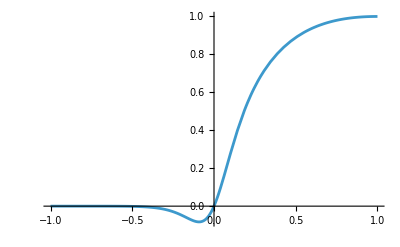

```mathematica
Plot[(2 g (1+g)^6)/(1+28 g^2+70 g^4+28 g^6+g^8),{g,-1,1}]
```

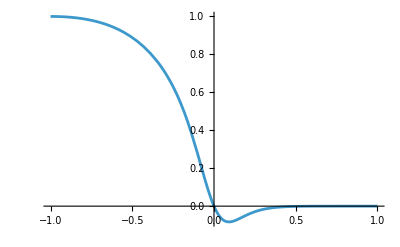

```mathematica
Plot[-(2 (-1+g)^6 g)/(1+28 g^2+70 g^4+28 g^6+g^8),{g,-1,1}]
```

## String operator from Transfer Matrices

Find left canonical form:

Form transfer map
	Ε = ∑_σ A_σ^†A_σ
	and find dominant left eigenvector/eigenmatrix

  ∑_σ A_σ^† l A_σ = η l

with η=1.

Then decompose l = R^†R:
first diagonalize l = U^†DU where D is a positive matrix 
due to construction of T. Then we have R=√D U.
I believe Cholesky gives the same.

We then define left-canonical form:
A_(L,σ):=R A R^†

From this one can show: that
∑_σ (A_(L,σ))^†A_(L,σ) = I

for right, do the same with
T = Ε^† = ∑_σ A_σ^†A_σ

```mathematica
toMat[A_]:=Flatten[A,{{1,2},{3,4}}];
```

```mathematica
(* Transfer matrices *)
(* T (α=0), EX (α=1), EY (α=2), EZ (α=3) *)
ET[α_]:=toMat@Table[Sum[PauliMatrix[α][[i+1,j+1]]M[i][[β1,α1]]Conjugate@M[j][[β2,α2]],{i,0,1},{j,0,1}],{α1,1,2},{α2,1,2},{β1,1,2},{β2,1,2}]//FullSimplify;
```

```mathematica
(*fixedPoints[T_]:=Module[{L={1/2,0,0,1/2},eigs,vecs,pos,R},{eigs,vecs}=Eigensystem[T];
pos=First@Ordering[Abs[eigs],-1];(*dominant eigenvalue index*)

R=vecs[[pos]];
R=R/(L.R);(*normalize so (L|R)=1*)
{L,R}];*)


indexAtOne[vals_,asm_]:=First@First@Position[Simplify[vals,Assumptions->asm],_?(TrueQ[#==1]&),{1}];

(* This version makes sure right index is chosen for g>0 and g<0 unlike simpler version above *)
fixedPoints[T_]:=Module[{valsL,vecsL,valsR,vecsR,iLpos,iLneg,iRpos,iRneg,Lpos,Lneg,Rpos,Rneg, L, R},

{valsR,vecsR}=Eigensystem[T];
{valsL,vecsL}=Eigensystem[ConjugateTranspose[T]];

(* Find dominating eigenvector *)
iRpos=indexAtOne[valsR,g>0];
iRneg=indexAtOne[valsR,g<0];
iLpos=indexAtOne[valsL,g>0];
iLneg=indexAtOne[valsL,g<0];

Rpos=vecsR[[iRpos]]//Simplify[#,Assumptions->g>0]&;
Rneg=vecsR[[iRneg]]//Simplify[#,Assumptions->g<0]&;
Lpos=vecsL[[iLpos]]//Simplify[#,Assumptions->g>0]&;
Lneg=vecsL[[iLneg]]//Simplify[#,Assumptions->g<0]&;

(* Normalize such that <L|R>= 1 *)
{Lpos,Rpos}={Lpos,Rpos/(Conjugate[Lpos].Rpos)};
    {Lneg,Rneg}={Lneg,Rneg/(Conjugate[Lneg].Rneg)};

L=Piecewise[{{Lpos,g>0},{Lneg,g<0}},Lpos];
     R=Piecewise[{{Rpos,g>0},{Rneg,g<0}},Rpos];

{L, R}//FullSimplify
]
```

```mathematica
fixedPoints[ET[0]]
```

{{1,0,0,1},Piecewise[{{{1/2,0,0,1/2}, g<0}, {{1/2,(√g)/(1+g),(√g)/(1+g),1/2}, True}}]}

```mathematica
S1Expectation[l_:5]:=Module[{T,EZ,EY,EX,L,R,val},
T=ET[0];
EX=ET[1];
EY=ET[2];
EZ=ET[3];

{L,R}=fixedPoints[T];
val=Conjugate[L].(MatrixPower[EX,l]).R;
val//Simplify
]
```

```mathematica
SZYExpectation[l_:5]:=Module[{T,EZ,EY,EX,L,R,val},
T=ET[0];
EX=ET[1];
EY=ET[2];
EZ=ET[3];

{L,R}=fixedPoints[T];
val=Conjugate[L].(EZ.EY.MatrixPower[EX,l-4].EY.EZ).R;
val//Simplify
]M[0]
```

```mathematica
S1exp = S1Expectation[5]//Simplify
```

Piecewise[{{(4 g)/(1+g)^2, g≥0}, {0, True}}]

```mathematica
SZYexp=SZYExpectation[5]//Simplify
```

Piecewise[{{-(4 g)/(-1+g)^2, g≤0}, {0, True}}]

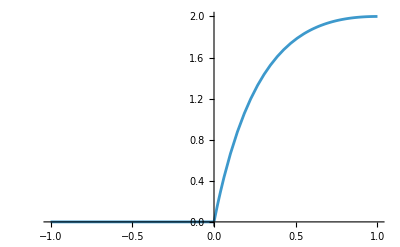

```mathematica
Plot[S1exp,{g,-1,1}]
```

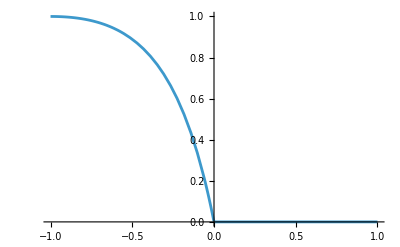

```mathematica
Plot[SZYexp,{g,-1,1}]
```

```mathematica
B1[0]:=1/Sqrt[2(1+Abs@g)]{Sqrt[Abs@g],1}
B1[1]:=1/Sqrt[2(1+Abs@g)]{1,Sign@g Sqrt[Abs@g]}
```

```mathematica
Table[
Sum[
M[σ][[a,b]] M[σ][[ap,bp]]  B1[σ1][[a]]B1[σ1][[ap]]

,{σ,0,1},{σ1,0,1},{a,1,2},{ap,1,2}],

{b,1,2},{bp,1,2}]//Simplify
```

{{1/2,Piecewise[{{(√g)/(1+g), g≥0}, {0, True}}]},{Piecewise[{{(√g)/(1+g), g≥0}, {0, True}}],1/2}}

```mathematica
V=Table[Sum[B1[σ][[b]]B1[σ][[bp]],{σ,0,1}],{b,1,2},{bp,1,2}]//Simplify
```

{{1/2,Piecewise[{{(√g)/(1+g), g≥0}, {0, True}}]},{Piecewise[{{(√g)/(1+g), g≥0}, {0, True}}],1/2}}

```mathematica
V/.g->1.2
```

{{1/2,0.49793},{0.49793,1/2}}

```mathematica
Tdo=Sum[ConjugateTranspose@M[σ].#.M[σ],{σ,0,1}]&
To=Sum[M[σ].#.ConjugateTranspose@M[σ],{σ,0,1}]&
```

∑_(σ=0)^1 ConjugateTranspose[M[σ]].#1.M[σ]&

∑_(σ=0)^1 M[σ].#1.ConjugateTranspose[M[σ]]&

```mathematica
To@IdentityMatrix[2]//Simplify
```

{{1,0},{0,1}}

```mathematica
Tdo@V-V//Simplify
```

{{0,0},{0,0}}

```mathematica
V/.g->1.2
```

{{1/2,0.49793},{0.49793,1/2}}

```mathematica
M[0]/.g->1.2//MatrixForm
```

(0.6742 | 0.738549
0 | 0)